```mathematica
SetDirectory[NotebookDirectory[]]
```

\\wsl.localhost\Ubuntu\home\shiyin\work\git\work\fluc_T\easyQCD\highorder\V2\MUB0\data

```mathematica
chi0=Flatten[Import["./chi0.dat"]];
chi1=Flatten[Import["./chi1.dat"]];
chi2=Flatten[Import["./chi2.dat"]];
chi3=Flatten[Import["./chi3.dat"]];
chi4=Flatten[Import["./chi4.dat"]];
chi5=Flatten[Import["./chi5.dat"]];
chi6=Flatten[Import["./chi6.dat"]];
T=Table[10+2i,{i,1,125}];
c1=chi1;
c2=T^2(1/chi2)^1;
c3=-T^5(1/chi2)^3(chi3);
c4=T^8(3(1/chi2)^5(chi3)^2-(1/chi2)^4 chi4);
c5=T^11(-15(1/chi2)^7(chi3)^3-(1/chi2)^5 chi5+10(1/chi2)^6 chi3 chi4);
c6=T^14(105(1/chi2)^9 chi3^4-105(1/chi2)^8 chi3^2 chi4+10(1/chi2)^7 chi4^2+15(1/chi2)^7 chi3 chi5-(1/chi2)^6 chi6);
```

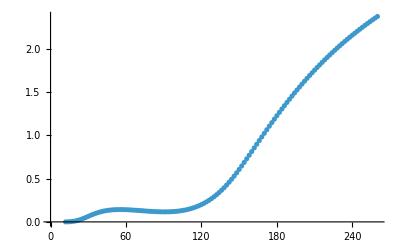

```mathematica
ListPlot[Transpose[{T,chi0/T^4}]]
```

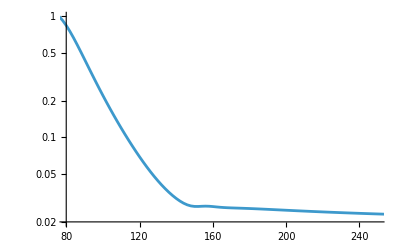

```mathematica
ListLinePlot[Transpose[{T,c2}],PlotRange->{{80,250},{0.02,1.}},ScalingFunctions->"Log"]
```

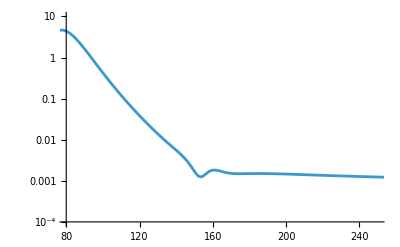

```mathematica
ListLinePlot[Transpose[{T,-c3}],PlotRange->{{80,250},{0.0001,10}},ScalingFunctions->"Log"]
```

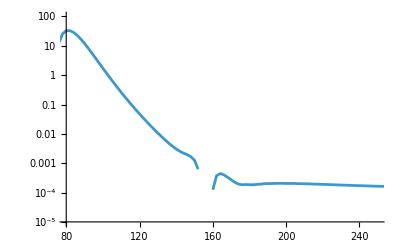

```mathematica
ListLinePlot[Transpose[{T,c4}],PlotRange->{{80,250},{0.00001,100}},ScalingFunctions->"Log"]
```

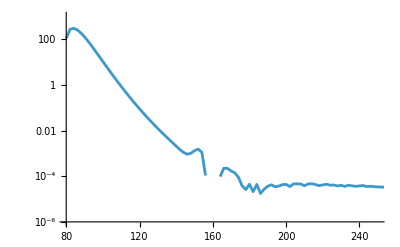

```mathematica
ListLinePlot[Transpose[{T,-c5}],PlotRange->{{80,250},{0.000001,1000}},ScalingFunctions->"Log"]
```

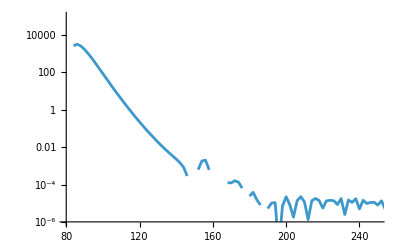

```mathematica
ListLinePlot[Transpose[{T,c6}],PlotRange->{{80,250},{10^-6,10^5}},ScalingFunctions->"Log"]
```